### Definitions

```mathematica
(* clear everything *)
ClearAll["Global`*"]
Remove["Global`*"]
```

```mathematica
(* Functions Definitions *)
```

```mathematica
l[z_]:=-z Log[1-ⅇ^(2π ⅈ z)]+ⅈ/2(π z^2+1/π PolyLog[2,ⅇ^(2π ⅈ z)])-(ⅈ π)/12
```

```mathematica
lAdjSU2[Δ_,u_]:=l[1-Δ]+l[1-Δ+2ⅈ u]+l[1-Δ-2ⅈ u]
```

```mathematica
lFundSU2[Δ_,u_]:=l[1-Δ+ⅈ u]+l[1-Δ-ⅈ u]
```

```mathematica
lFundU1[Δ_,u_]:=l[1-Δ+ⅈ u]
```

```mathematica
lAdjU1[Δ_]:=l[1-Δ]
```

```mathematica
lBiFundSU2U1[Δ_,u1_,u2_]:=l[1-Δ+ⅈ (u1+u2)]+l[1-Δ+ⅈ (u1-u2)]
```

```mathematica
uMax=1;
```

```mathematica
zSSQs0Integrand[g_,a_,u_]:=Module[
{ΔQ,ΔQtilde,ΔPhi},
ΔQ=1/2+a;ΔQtilde=1/2+a;ΔPhi=1-2a;
(Sinh[2 π u])^2 Exp[g lAdjSU2[ΔQ,u]+g lAdjSU2[ΔQtilde,u]+ lAdjSU2[ΔPhi,u]]
]
```

```mathematica
zSSQs0[g_,a_]:=Module[
{ΔQ,ΔQtilde,ΔPhi},
ΔQ=1/2+a;ΔQtilde=1/2+a;ΔPhi=1-2a;
NIntegrate[(Sinh[2 π u])^2 Exp[g lAdjSU2[ΔQ,u]+g lAdjSU2[ΔQtilde,u]+ lAdjSU2[ΔPhi,u]],{u,-uMax,uMax}]//Quiet
]
```

```mathematica
zTSU2[a_]:=Module[
{ΔQ,ΔQtilde,ΔPhi},
ΔQ=1/2+a;ΔQtilde=1/2+a;ΔPhi=1-2a;
Exp[lAdjU1[ΔPhi]] NIntegrate[
Exp[ lBiFundSU2U1[ΔQ,u1,0]+lBiFundSU2U1[ΔQtilde,-u1,0]],{u1,-uMax,uMax}
]//Quiet
]
```

```mathematica
zSSQs1[g_,a_]:=Module[
{ΔQ,ΔQtilde,ΔPhi},
ΔQ=1/2+a;ΔQtilde=1/2+a;ΔPhi=1-2a;
Exp[lAdjU1[ΔPhi]]  NIntegrate[
Exp[ lBiFundSU2U1[ΔQ,u1,u2]+lBiFundSU2U1[ΔQtilde,-u1,u2]]
(Sinh[2 π u2])^2 Exp[g lAdjSU2[ΔQ,u2]+g lAdjSU2[ΔQtilde,u2]+ lAdjSU2[ΔPhi,u2]]
,{u1,-uMax,uMax},{u2,-uMax,uMax}]//Quiet
]
```

```mathematica
(* Plot function *)
```

```mathematica
plotZ[deltaVec_,zVec_]:=(
data=Table[{deltaVec⟦i⟧,zVec⟦i⟧},{i,1,vecLen}];
plot1=ListPlot[data];
indMin=Position[zVec,Min[zVec]];
deltaMin=deltaVec⟦indMin⟦1⟧⟧;
plot2=ListPlot[{{deltaMin⟦1⟧,Min[zVec]}},PlotStyle->{Red,Thick,PointSize[Large]}];
Show[plot1,plot2,Frame->True,ImageSize->300,GridLines->Automatic]
)
```

```mathematica
(* Axis definitions *)
```

```mathematica
vecLen=20;
r1=-0.3; r2=0.3; 
xVec=r1+Range[vecLen]/vecLen*(r2-r1)+ϵ;
aMaxRange=1;
cons={Abs[a]<aMaxRange};
```

### SSQ N=2,s=0,g=1 Integrand

Integrand as a function of u (for g=1, a=0.001):

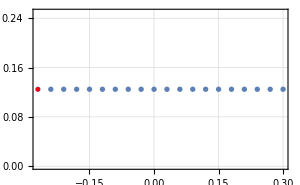

```mathematica
g=1;
a=0.001;
Print["Integrand as a function of u (for g=", g, ", a=", a, "):"]
zVec=Table[Abs[zSSQs0Integrand[g,a,u]],{u,1,vecLen}];
plotZ[xVec,zVec]
```

### SSQ N=2,s=0,g=2

Function of a:

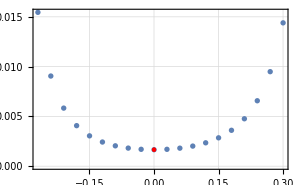

```mathematica
g=2;
Print["Function of a:"]
zVec=Table[Abs[zSSQs0[g,xVec⟦i⟧]],{i,1,vecLen}];
plotZ[xVec,zVec]
```

### SSQ N=2,s=0,g=3

Function of a:

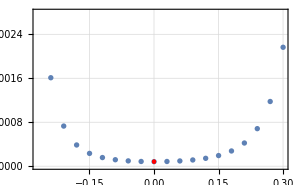

```mathematica
g=3;
Print["Function of a:"]
zVec=Table[Abs[zSSQs0[g,xVec⟦i⟧]],{i,1,vecLen}];
plotZ[xVec,zVec]
```

### SSQ N=2,s=0,g=4

Function of a:

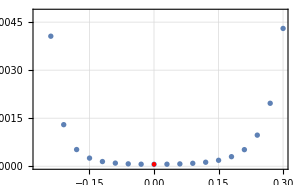

```mathematica
g=4;
Print["Function of a:"]
zVec=Table[Abs[zSSQs0[g,xVec⟦i⟧]],{i,1,vecLen}];
plotZ[xVec,zVec]
```

### TSU(2)

Function of a:

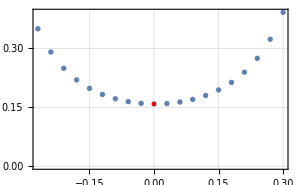

```mathematica
Print["Function of a:"]
zVec=Table[Abs[zTSU2[xVec⟦i⟧]],{i,1,vecLen}];
plotZ[xVec,zVec]
```

Function of a:

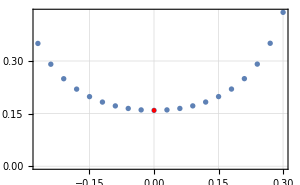

```mathematica
(* convergence test in uMax *)
uMax=10;
Print["Function of a:"]
zVec=Table[Abs[zTSU2[xVec⟦i⟧]],{i,1,vecLen}];
plotZ[xVec,zVec]
uMax=1;
```

### SSQ N=2,s=1,g=1

Function of a:

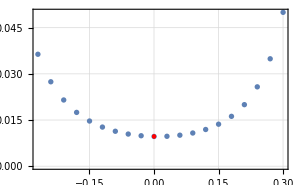

```mathematica
g=1;
Print["Function of a:"]
zVec=Table[Abs[zSSQs1[g,xVec⟦i⟧]],{i,1,vecLen}];
plotZ[xVec,zVec]
```

Function of a:

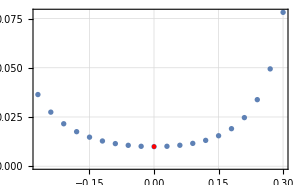

```mathematica
(* convergence test in uMax *)
g=1;
uMax=3;
Print["Function of a:"]
zVec=Table[Abs[zSSQs1[g,xVec⟦i⟧]],{i,1,vecLen}];
plotZ[xVec,zVec]
uMax=1;
```

### SSQ N=2,s=1,g=2

Function of a:

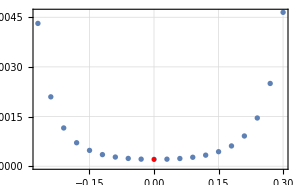

```mathematica
g=2;
Print["Function of a:"]
zVec=Table[Abs[zSSQs1[g,xVec⟦i⟧]],{i,1,vecLen}];
plotZ[xVec,zVec]
```

### SSQ N=2,s=1,g=3

Function of a:

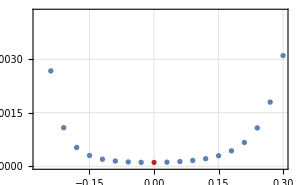

```mathematica
g=3;
Print["Function of a:"]
zVec=Table[Abs[zSSQs1[g,xVec⟦i⟧]],{i,1,vecLen}];
plotZ[xVec,zVec]
```

### SSQ N=2,s=1,g=4

Function of a:

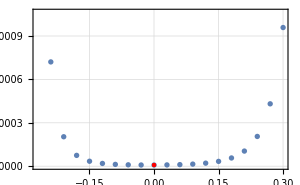

```mathematica
g=4;
Print["Function of a:"]
zVec=Table[Abs[zSSQs1[g,xVec⟦i⟧]],{i,1,vecLen}];
plotZ[xVec,zVec]
```